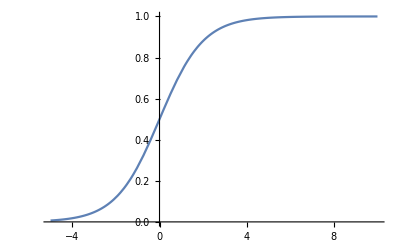

```mathematica
Plot[Exp[x]/(1+Exp[x]),{x, -5, 10}]
```

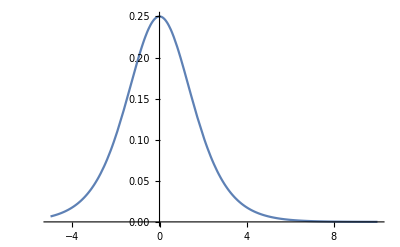

```mathematica
Plot[Exp[x]/(1+Exp[x])^2,{x, -5, 10}]
```

```mathematica
D[(1-i+i*Exp[t])^n(1-j+j*Exp[t])^n, t]
```

ⅇ^t (1-i+ⅇ^t i)^n j (1-j+ⅇ^t j)^(-1+n) n+ⅇ^t i (1-i+ⅇ^t i)^(-1+n) (1-j+ⅇ^t j)^n n

```mathematica
D[(1-i+i*Exp[t])^n(1-j+j*Exp[t])^n, {t,2}]
```

2 ⅇ^(2 t) i (1-i+ⅇ^t i)^(-1+n) j (1-j+ⅇ^t j)^(-1+n) n^2+(1-j+ⅇ^t j)^n (ⅇ^t i (1-i+ⅇ^t i)^(-1+n) n+ⅇ^(2 t) i^2 (1-i+ⅇ^t i)^(-2+n) (-1+n) n)+(1-i+ⅇ^t i)^n (ⅇ^t j (1-j+ⅇ^t j)^(-1+n) n+ⅇ^(2 t) j^2 (1-j+ⅇ^t j)^(-2+n) (-1+n) n)

```mathematica
m1 [t_]:= Simplify[ⅇ^t (1-i+ⅇ^t i)^n j (1-j+ⅇ^t j)^(-1+n) n+ⅇ^t i (1-i+ⅇ^t i)^(-1+n) (1-j+ⅇ^t j)^n n]
```

```mathematica
m1[0]
```

(i+j) n

```mathematica
m2[t_]:= Simplify[2 ⅇ^(2 t) i (1-i+ⅇ^t i)^(-1+n) j (1-j+ⅇ^t j)^(-1+n) n^2+(1-j+ⅇ^t j)^n (ⅇ^t i (1-i+ⅇ^t i)^(-1+n) n+ⅇ^(2 t) i^2 (1-i+ⅇ^t i)^(-2+n) (-1+n) n)+(1-i+ⅇ^t i)^n (ⅇ^t j (1-j+ⅇ^t j)^(-1+n) n+ⅇ^(2 t) j^2 (1-j+ⅇ^t j)^(-2+n) (-1+n) n)]
```

```mathematica
m2[0]
```

n (i+j+i^2 (-1+n)+j^2 (-1+n)+2 i j n)

```mathematica
Simplify[m2[0]-(m1[0])^2]
```

(i-i^2+j-j^2) n